```mathematica
(* Jai Prasadh *)
(* Code for problem 1, HW3 *)

m:=.2 
k:=7.2
x0:=0
v0 := 0
w0 := 6
w := 15
F0 := 8
gamma := 1.2
A:= .211
delta := 3.05

NDSolve[{x''[t]+(gamma)x'[t] + (w0^2) x[t]==(F0 / m) Cos[w*t],x[0]==x0,x'[0]==v0},x,{t,0,10}];

f[t_]=x[t]/.%;                                (* Solution given initial conditions *)
g[t_] = (A) Cos[w*t - delta];   (* Steady state solution *)

h[t_] = f[t] - g[t];
```

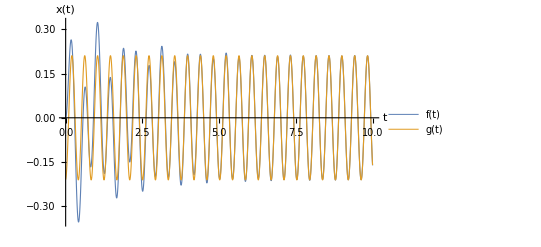
-Graphics- -Graphics-

```mathematica
Plot[{f[t], g[t]},{t,0,10},AxesLabel->{"t","x(t)"},PlotStyle->Thickness[0.002],AxesStyle->Directive[Thickness[0.002],14], PlotLegends->"Expressions"]

Plot[h[t],{t,0,10},AxesLabel->{"t","x(t)"},PlotStyle->Thickness[0.002],AxesStyle->Directive[Thickness[0.002],14], PlotLegends->"Expressions"]
```

```mathematica
.02 * A;
FindRoot[h[t]== .02 * A, {t, 6}]
tsteady = t /. %;
tsteady / ( 1/gamma)
```

{t→6.21689}

7.46026

Null